## Chapter 2 Problem 34: Delta Function Potentials

```mathematica
Remove["Global`*"]
```

```mathematica
$Assumptions=α>0&&a>0&&b>0&&Subscript[V, 0]>0&&ℏ>0&&m>0;
```

First do the single delta function potential. Write out the obvious forms, and scale the potential by the “strength” b. Note that b has dimensions of length.

```mathematica
uNeg=A Exp[α x];
uPos=A Exp[-α x];
```

```mathematica
valV0=ℏ^2β^2/(m b^2)
```

(β^2 ℏ^2)/(b^2 m)

Integrate the Schrodinger Equation over the delta function

```mathematica
uInt=(D[uPos,x]/.x->0)-(D[uNeg,x]/.x->0);
intSE=-(ℏ^2/(2m))uInt-(Subscript[V, 0] b uPos/.x->0/.Subscript[V, 0]->valV0)==0;
sol=Solve[intSE,α]
```

{{α→β^2/b}}

There is only one solution, and the bound state energy is determined.

```mathematica
energy=-ℏ^2α^2/(2 m)/.sol[[1]]
```

-(β^4 ℏ^2)/(2 b^2 m)

Construct, normalize and plot the wave function. Use the distance scale b to have a dimensionless position y=x/b. For the plot, use β=1.

```mathematica
uFull=Piecewise[{{uNeg/.x->b y,y<-0},{uPos/.x->b y,y>0}}];
norm=Solve[Integrate[uFull,{y,-∞,∞}]==1,A][[1]]
```

{A→(b α)/2}

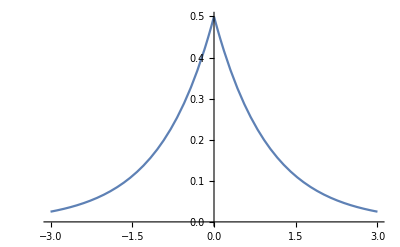

```mathematica
uFullNorm=uFull/.norm/.sol/.Subscript[V, 0]->valV0/.β->1;
Plot[uFullNorm,{y,-3,3},PlotRange->{0,0.5}]
```

Now do the double delta function, all the same, except an extra equation. Start from scratch.

```mathematica
Remove["Global`*"]
$Assumptions=α>0&&a>0&&b>0&&Subscript[V, 0]>0&&ℏ>0&&m>0 && z>0 && β>0;
```

Here use the distance scale of the individual potential delta functions, namely b/2, and include a parameter β that can be used to vary the strength of the potential, while keeping b fixed.

```mathematica
valV0=ℏ^2β^2/(m a (b/2));
```

This time there are three regions to consider. We continue to write the energy eigenvalue as -ℏ^2α^2/2 m.

```mathematica
uMid=A Exp[α x]+B Exp[-α x];
uNeg=C Exp[α x];
uPos=D Exp[-α x];
```

Use wave function continuity to get C and D in terms of A and B

```mathematica
solC=Solve[(uMid/.x->-a/2)==(uNeg/.x->-a/2),C][[1]]
solD=Solve[(uMid/.x->a/2)==(uPos/.x->a/2),D][[1]]
```

{C→A+B ⅇ^(a α)}

{D→B+A ⅇ^(a α)}

Now do the integral over each delta function to get two more equations.

```mathematica
uInt=(D[uMid,x]/.x->-a/2)-(D[uNeg,x]/.x->-a/2);
intSEL=Simplify[
-(ℏ^2/(2m))(uInt/.solC)-((Subscript[V, 0]/.Subscript[V, 0]->valV0)(b/2) uMid/.x->-a/2)==0]
```

a B ⅇ^(a α) α==(A+B ⅇ^(a α)) β^2

```mathematica
uInt=(D[uPos,x]/.x->a/2)-(D[uMid,x]/.x->a/2);
intSER=Simplify[
-(ℏ^2/(2m))(uInt/.solD)-((Subscript[V, 0]/.Subscript[V, 0]->valV0)(b/2) uMid/.x->a/2)==0]
```

a A ⅇ^(a α) α==(B+A ⅇ^(a α)) β^2

Find the factors of the determinant of the coefficient matrix

```mathematica
mat=Normal[CoefficientArrays[{intSEL,intSER},{A,B}]][[2]];
det=Det[mat];
factors=FactorList[det];
fac1=factors[[2]][[1]]
fac2=factors[[3]][[1]]
```

a ⅇ^(a α) α-β^2-ⅇ^(a α) β^2

a ⅇ^(a α) α+β^2-ⅇ^(a α) β^2

Define z=aα

```mathematica
fac1z=fac1/.a->z/α;
fac2z=fac2/.a->z/α;
```

We want to find the value of z that makes each of the factors equal to zero, thus making the determinant zero. First, though, let’s make some plots for different values of the potential strength β to see if there are always two solutions

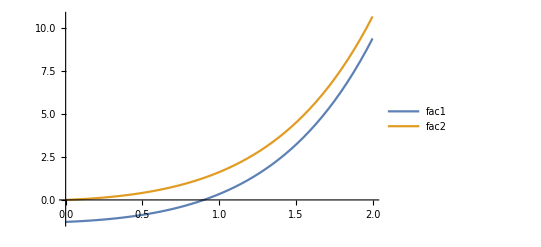

```mathematica
βSub=0.8;
Plot[{fac1z/.β->βSub,fac2z/.β->βSub},{z,0,2},PlotLegends->{"fac1","fac2"}]
```

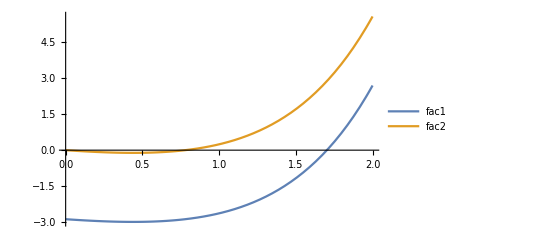

```mathematica
βSub=1.2;
Plot[{fac1z/.β->βSub,fac2z/.β->βSub},{z,0,2},PlotLegends->{"fac1","fac2"}]
```

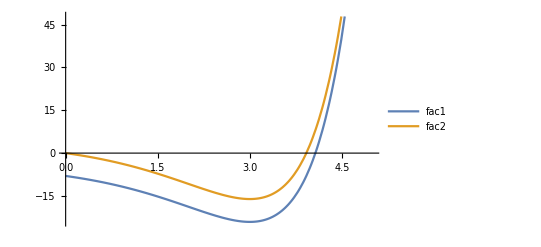

```mathematica
βSub=2;
Plot[{fac1z/.β->βSub,fac2z/.β->βSub},{z,0,5},PlotLegends->{"fac1","fac2"}]
```

It looks as if there are two solutions so long as β is larger than something close to unity. Also, the two solutions get very close to each other as β increases. Let’s try and understand this from the formulas.

```mathematica
z1=z/.Solve[fac1z==0,z][[1]]
z2=z/.Solve[fac2z==0,z][[1]]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

β^2+ProductLog[ⅇ^(-β^2) β^2]

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

β^2+ProductLog[-ⅇ^(-β^2) β^2]

ProductLog[x] returns the solution w to the equation x=wExp[w]. For large β, the argument of ProductLog is zero, and the solution to 0=wExp[w] is w=0, so both solutions for z=αa are close to β^2. This is confirmed from the plot above, even for the not-so-large value β=2.

Now try plotting the two solutions for zero determinant as a function of β for small β.

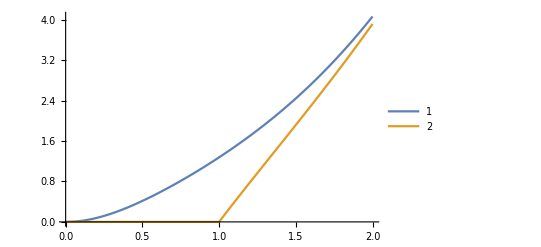

```mathematica
Plot[{z1,z2},{β,0,2},PlotLegends->{1,2}]
```

So, no root is found for the second equation if β is less than unity. Let’s make a plot that shows both these behaviors.

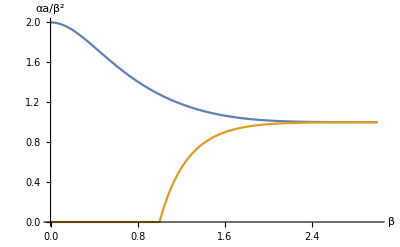

```mathematica
Plot[{z1/β^2,z2/β^2},{β,0,3},AxesLabel->{"β","αa/β^2"}]
```

We are informed by the documentation that when the argument of ProductLog is -1/e or less, there are no real solutions. For us, the argument of the second factor is -Exp[-β^2]β^2 so that’s what’s going on at β=1. So, when the well depth is less than ...

```mathematica
valV0/.β->1
```

(2 ℏ^2)/(a b m)

... there will only be one eigenvalue.  This will always be the case as a goes to zero.

Let’s now take a look at the wave functions above and below the critical well depth. I don’t see how to do this symbolically, given the peculiar behavior of ProductLog, so we’ll evaluate the wave functions (and find the eigenvalues) for specific values of β.

First we need to find B in terms of A

```mathematica
solBa=Solve[(mat[[1]].{A,B})==0,B];
solBb=Solve[(mat[[2]].{A,B})==0,B];
```

Let’s make sure these give the same result for B when we are at an eigenvalue

```mathematica
B/.solBa/.α->z1/a/.A->1/.β->2.0
B/.solBb/.α->z1/a/.A->1/.β->2.0
```

{1.}

{1}

Form the wave functions so that there is only one coefficient, A

```mathematica
solB=solBa;
uNegA=uNeg/.solC/.solB;
uMidA=uMid/.solB;
uPosA=uPos/.solD/.solB;
```

Choose a value for β above the critical value, normalize the wave functions, and plot them

```mathematica
βVal=1.5;
z1β=z1/.β->βVal
z2β=z2/.β->βVal
```

2.44511

1.9202

```mathematica
uNegA1=uNegA/.α->z1β/a/.β->βVal/.x->y a;
uMidA1=uMidA/.α->z1β/a/.β->βVal/.x->y a;
uPosA1=uPosA/.α->z1β/a/.β->βVal/.x->y a;
```

```mathematica
uA1=Piecewise[
{{uNegA1,y<-1/2},
{uMidA1,y>-1/2&&y<1/2},
{uPosA1,y>1/2}}];
u1={uA1/.Solve[Integrate[uA1^2,{y,-∞,∞}]==1,A][[2]]};
```

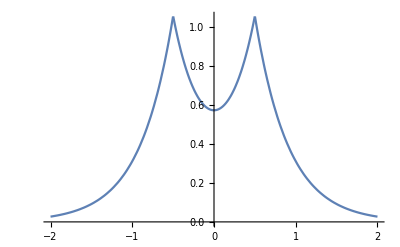

```mathematica
Plot[u1,{y,-2,2}]
```

```mathematica
uNegA2=uNegA/.α->z2β/a/.β->βVal/.x->y a;
uMidA2=uMidA/.α->z2β/a/.β->βVal/.x->y a;
uPosA2=uPosA/.α->z2β/a/.β->βVal/.x->y a;
```

```mathematica
uA2=Piecewise[
{{uNegA2,y<-1/2},
{uMidA2,y>-1/2&&y<1/2},
{uPosA2,y>1/2}}];
u2={uA2/.Solve[Integrate[uA2^2,{y,-∞,∞}]==1,A][[1]]};
```

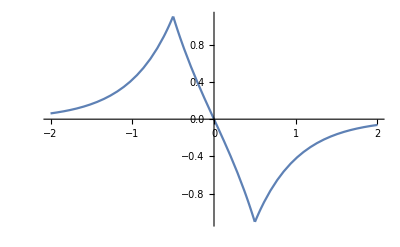

```mathematica
Plot[u2,{y,-2,2}]
```

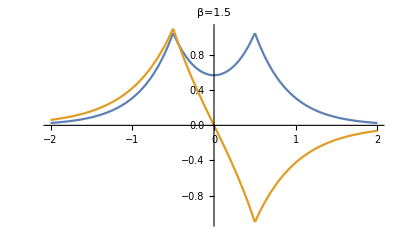

```mathematica
Plot[{u1,u2},{y,-2,2},PlotLabel->"β=1.5"]
```

Now choose a value for β below the critical value

```mathematica
βVal=0.25;
z1β=z1/.β->βVal
```

0.118041

```mathematica
uNegA1=uNegA/.α->z1β/a/.β->βVal/.x->y a;
uMidA1=uMidA/.α->z1β/a/.β->βVal/.x->y a;
uPosA1=uPosA/.α->z1β/a/.β->βVal/.x->y a;
```

```mathematica
uA1=Piecewise[
{{uNegA1,y<-1/2},
{uMidA1,y>-1/2&&y<1/2},
{uPosA1,y>1/2}}];
u1={uA1/.Solve[Integrate[uA1^2,{y,-∞,∞}]==1,A][[2]]};
```

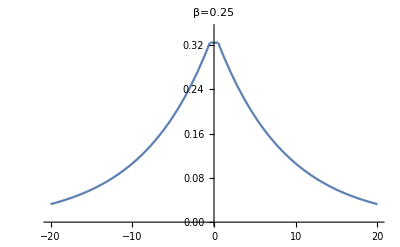

```mathematica
Plot[u1,{y,-20,20},PlotRange->{0,0.35},PlotLabel->"β=0.25"]
```

The wave function seems to approach the result for a single δ-function. This makes sense because...

```mathematica
valV0/.β->β1 Sqrt[a/(2b)]
```

(β1^2 ℏ^2)/(b^2 m)

... is the same scaled form for V0 that we used for the single δ-function potential, and β→0 as a→0 with β1 fixed. To check that we get the same eigenvalue for a single δ-function as a→0, expand z1 for small β.

```mathematica
αVal=Normal[Series[z1,{β,0,2}]]/a/.β->β1 Sqrt[a/(2b)]
```

β1^2/b

```mathematica
energy=-ℏ^2α^2/(2 m)/.α->αVal
```

-(β1^4 ℏ^2)/(2 b^2 m)

This is indeed the same energy eigenvalue that we got in the case of a single δ-function